```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX

## Vegas Grids

```mathematica
nrfiles=10;
nrbins=100;
```

```mathematica
Grids=Table[Get["VegasGrids/Step"<>ToString[i]<>".txt"],{i,1,nrfiles}];
```

```mathematica
Grids2=Table[Table[Mean/@Grids[[i,j]],{j,1,Length[Grids[[i]]]}],{i,1,Length[Grids]}];
```

```mathematica
Grids3=Table[Table[1/(#[[2]]-#[[1]])&/@Grids[[i,j]],{j,1,Length[Grids[[i]]]}],{i,1,Length[Grids]}];
```

```mathematica
Grids2//Dimensions
```

{10,2,100}

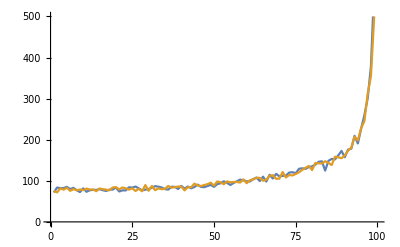

```mathematica
pos=nrfiles;
ListLinePlot[{Grids3[[pos,1]],Grids3[[pos,2]](*,Grids3[[pos,3]]*)},PlotRange->{0,500}]
```

### x1

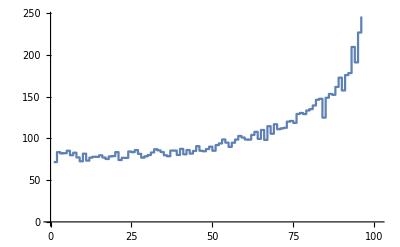

```mathematica
ListStepPlot[Grids3[[pos,1]]]
```

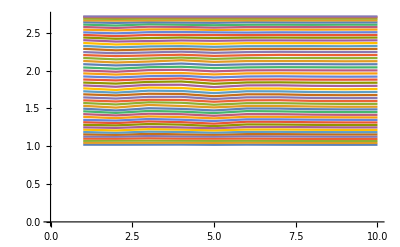

```mathematica
var=1;
ListLinePlot[Table[Exp/@Grids2[[;;,var,2i]],{i,1,nrbins/2}]]
```

### x2

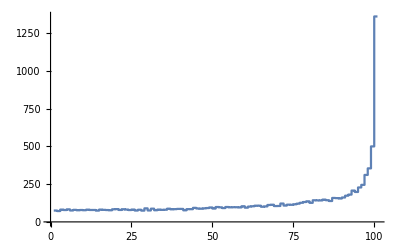

```mathematica
ListStepPlot[Grids3[[pos,2]],PlotRange->All]
```

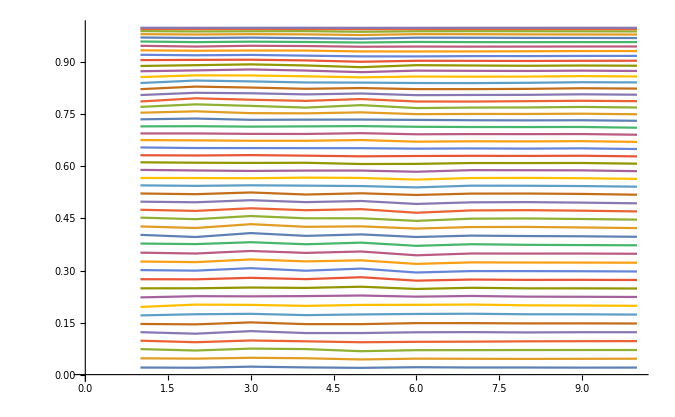

```mathematica
var=2;
ListLinePlot[Table[Grids2[[;;,var,2i]],{i,1,nrbins/2}]]
```

### Y=a x+c

```mathematica
ListStepPlot[Grids3[[pos,3]]]
```

Part::partw: Part 3 of {{71.6428,83.5426,82.031,82.2714,85.2144,79.8657,82.8729,77.2312,72.5794,81.6807,73.3462,76.9917,78.0243,77.8493,79.7381,77.1404,75.3109,78.4203,78.8094,83.5629,«12»,85.6991,83.6496,79.7907,78.6174,85.4141,85.4182,80.138,87.454,80.9541,86.0834,81.7692,84.9761,90.6806,85.1799,84.5745,87.2444,90.1058,85.2014,«50»},{«1»}} does not exist.

ListStepPlot::lpn: {«1»}⟦10,3⟧ is not a list of numbers or pairs of numbers.

ListStepPlot[{{{66.2451,85.6394,78.8693,89.4208,83.9546,68.1649,77.671,80.5214,83.1108,79.2609,75.1513,79.091,78.646,74.0302,73.9977,80.4448,84.5602,74.397,80.3686,70.9578,78.1908,78.3796,97.7789,72.1436,63.4426,78.1165,77.7268,77.4584,75.5407,82.3323,80.9673,96.6789,71.3535,90.774,75.567,92.1681,91.5489,83.0931,87.6767,82.2812,85.1108,74.4825,97.1239,78.2924,101.638,82.3933,95.3801,99.1924,97.8154,89.5347,90.5884,97.5609,93.6949,93.6281,100.267,90.3754,117.573,97.1286,102.407,98.8123,90.4356,102.489,90.2424,117.216,109.276,100.859,118.314,121.372,109.199,108.849,105.098,106.414,130.257,117.901,121.646,117.244,130.414,134.869,135.868,149.894,145.995,133.072,151.577,146.74,131.198,161.92,140.897,144.118,169.084,165.902,166.868,186.584,232.499,220.629,210.506,232.796,244.472,478.054,661.686,1334.09},{66.4607,93.6148,72.41,67.1237,71.6941,97.3114,75.5355,85.0295,78.8929,83.8569,88.9464,76.5864,79.1348,90.5087,82.4116,75.0372,71.5075,72.7001,78.1743,77.1091,80.9076,67.8217,77.1896,83.1827,80.5909,78.9215,81.2439,72.6939,76.6374,79.7678,75.8012,89.0819,78.7491,83.7483,71.5405,92.2751,81.0653,102.22,78.5937,87.0436,80.2805,92.7373,86.6208,77.4755,97.5634,106.537,77.6748,88.0745,91.2017,96.0008,92.8292,113.33,81.7922,86.2746,94.9165,102.369,107.406,99.7098,103.66,87.7803,100.343,108.432,100.383,110.883,118.312,129.335,139.348,111.111,99.1028,125.228,117.412,112.216,109.985,121.437,116.957,111.776,124.845,117.832,133.855,141.32,120.399,99.3575,156.496,126.097,175.162,155.923,154.859,151.897,164.748,161.338,176.763,183.923,221.697,203.284,214.322,300.37,289.54,419.852,573.73,1597.1}},{{72.0208,74.2093,84.6943,79.0253,73.4784,80.7983,85.5578,84.1647,82.7684,82.0182,98.6823,96.0356,83.7184,77.7568,75.3697,83.6079,65.8904,81.4148,68.5549,84.7816,80.0907,98.1711,75.0184,74.5814,96.0929,77.9415,74.2356,84.8001,75.8001,103.768,85.4234,89.5257,75.9391,75.3719,74.9842,71.5195,83.6591,80.7406,83.9531,85.9832,75.0369,84.6077,94.9255,98.4461,95.1201,95.998,79.7624,80.6291,91.2648,85.6056,92.2751,79.9554,107.131,104.833,98.1588,96.8909,110.073,106.097,103.062,93.6281,90.6771,102.031,104.486,120.972,92.8256,103.543,96.9915,110.652,120.993,115.828,134.394,90.3333,131.131,124.887,130.184,111.819,128.793,119.844,131.058,140.94,144.247,127.713,138.397,138.537,123.118,142.934,158.501,156.89,155.366,181.57,151.3,130.219,184.692,212.596,243.231,240.239,232.1,332.244,523.95,1104.7},{80.3633,67.3984,80.9241,78.0311,83.0704,99.8407,80.6568,77.3781,83.8215,80.4241,73.4999,71.1651,69.0781,64.8959,74.5961,74.6957,82.3042,92.4578,86.1661,87.1878,79.0348,67.2674,87.4773,80.9271,80.6355,84.1633,84.4439,71.2315,66.2138,98.0668,107.776,83.4932,77.7497,69.656,82.8628,80.8725,87.4314,80.3063,77.024,88.4421,80.3474,96.1779,82.7728,74.6139,95.8044,92.9554,89.494,93.6849,85.6845,93.7625,101.137,90.0462,95.4697,91.4124,84.8591,102.529,97.8991,102.626,91.8731,98.4638,102.931,68.6136,117.799,98.6033,95.4811,109.222,120.768,110.289,132.166,133.353,108.301,102.363,111.462,137.189,127.858,143.003,143.955,131.265,142.523,118.294,130.895,147.833,153.81,148.954,154.576,148.74,171.49,181.459,146.43,153.541,162.217,196.972,204.021,194.79,240.507,247.174,279.406,340.525,632.077,1292.05}},{{65.9521,78.9345,83.3469,91.5741,73.497,63.8474,74.1697,70.4156,77.3141,77.8494,77.7284,83.149,85.8669,70.6702,68.3899,89.6611,75.8684,78.4759,63.5654,75.9708,73.2645,80.6421,89.188,79.2981,83.1271,77.9998,73.3723,98.6991,68.56,85.9621,78.6471,92.2354,61.9821,73.8167,89.5157,105.336,89.5668,102.323,79.861,79.8123,87.3758,75.2814,88.3635,84.185,84.977,86.6638,99.6927,111.742,84.8065,103.857,102.397,95.2674,94.7967,114.916,97.7481,96.8551,96.5559,91.6808,109.644,111.53,126.353,110.224,111.98,90.3395,107.187,128.874,103.197,100.117,116.278,115.72,116.105,109.781,113.442,120.744,123.952,137.433,159.021,115.472,121.869,125.789,121.221,118.253,147.998,131.927,144.184,136.164,141.11,155.982,152.766,174.908,205.634,199.669,229.807,222.829,199.401,277.583,269.54,358.961,633.583,1182.53},{61.1306,75.9425,77.9538,81.5107,68.7661,85.7313,90.0739,77.5112,70.6821,78.3896,80.7515,77.8784,83.2981,80.0831,77.9803,73.6482,80.9103,93.0123,75.0011,74.8676,70.5205,70.0707,66.8132,86.9007,81.338,70.9508,91.3847,77.1691,83.9516,73.1444,75.8667,79.1369,79.3168,74.349,96.2107,78.446,94.7935,92.65,84.8714,81.7757,90.7789,96.1445,98.3598,95.4534,101.213,93.8776,90.5965,107.808,78.9418,85.7505,97.5243,78.5744,110.338,103.856,91.2438,93.438,107.24,96.7241,95.7257,95.2236,109.064,94.7114,122.347,87.3093,91.606,115.308,108.065,121.82,96.8978,117.955,133.353,106.286,118.199,108.851,121.484,117.74,118.984,106.53,146.362,159.656,156.608,127.329,157.193,142.411,167.343,154.239,132.379,177.04,172.831,152.997,168.772,206.886,184.698,228.619,236.7,268.897,270.168,400.257,626.67,1369.1}},{{64.0282,74.9112,85.8591,87.9547,77.6354,77.9178,83.3392,73.1428,80.6744,78.3415,85.3971,81.0766,69.8784,75.2795,71.6146,94.3814,81.9214,87.2697,61.3738,69.2493,84.8727,78.3331,91.6274,75.6694,79.5705,71.7128,70.9429,93.9909,87.8408,71.056,89.4605,79.0603,77.9797,79.2947,70.6536,74.0147,92.339,82.0438,75.7575,85.0274,93.1562,81.1874,88.0849,95.2708,84.287,89.6931,80.0668,88.0652,83.261,87.0495,91.9526,109.113,107.225,102.06,114.178,100.161,94.4625,87.6911,104.565,107.874,97.9497,89.3926,94.1951,105.011,142.047,119.559,112.258,118.192,106.413,110.716,126.689,136.095,128.216,118.41,131.641,125.52,122.531,127.091,118.127,137.059,136.701,142.554,131.492,125.71,153.686,140.079,156.957,191.662,166.736,197.418,174.911,198.094,162.822,212.942,226.915,242.,363.097,345.046,479.01,1050.89},{70.1494,76.4095,73.0954,81.4121,69.1804,85.9166,87.2069,97.813,81.895,77.301,84.1058,67.5799,79.8304,82.8372,75.3503,67.7209,70.4923,75.9447,88.0979,87.7543,71.5717,89.6354,80.4874,80.1584,70.7263,76.8122,81.5868,87.1093,79.5467,75.8312,86.216,83.845,73.7444,75.8142,85.5429,80.5858,85.7224,90.9057,84.4385,84.1796,94.0966,93.2591,76.3209,70.2333,94.8298,91.8528,103.604,95.8566,87.9163,84.4011,97.599,115.769,86.0427,88.2944,93.2741,101.431,111.082,87.4059,87.9142,105.711,96.2364,116.559,110.305,103.695,133.807,116.391,101.155,96.9492,108.321,116.366,127.997,123.577,95.0953,136.19,102.645,115.306,122.895,122.504,141.199,142.758,127.007,157.682,141.742,141.076,127.503,150.432,152.84,161.263,171.958,180.025,192.978,158.751,190.442,200.075,208.699,253.46,337.677,372.628,573.827,1613.4}},{{75.9676,78.1514,87.8187,77.1706,78.4882,76.0057,71.233,88.759,76.2856,91.2589,84.3385,101.493,78.798,86.3455,80.3545,75.9248,91.8384,84.7159,90.1953,82.8578,82.4916,74.4566,80.2161,66.4788,87.3538,72.651,90.2259,74.0662,80.4955,82.5766,89.9087,74.4817,77.0601,71.1456,94.567,94.1961,72.6656,78.9901,98.5246,84.4816,84.0532,103.912,73.7187,86.2111,85.4061,90.607,87.7975,86.7903,77.9475,86.6168,98.9478,80.0048,94.4422,86.6594,101.29,97.4753,93.5707,102.12,95.8214,81.3597,111.61,109.627,91.3717,115.748,104.736,109.168,115.618,99.3014,114.77,111.519,107.035,114.292,131.557,99.3915,137.559,114.849,125.453,114.023,135.421,121.507,133.828,126.204,140.665,155.173,162.738,151.832,177.808,157.075,160.215,177.731,161.532,154.325,185.761,203.354,211.966,218.225,308.235,320.68,610.675,1053.84},{77.9706,75.0958,81.1595,96.0738,82.2669,77.3728,75.5619,81.7947,68.5227,85.5922,79.7328,68.6798,72.4397,72.5333,75.5814,68.11,70.1774,91.4985,76.6242,73.2528,72.3212,74.6016,78.0914,92.9188,82.2869,79.5558,72.9396,91.2907,74.3684,75.5145,81.9221,101.713,77.442,93.4497,84.6766,81.7862,72.4899,78.406,81.7396,101.173,84.3276,92.931,97.4519,95.9803,83.6079,80.7031,100.116,98.0273,118.47,93.7074,85.5686,96.8903,79.9671,86.0096,84.5878,86.5011,98.5984,127.59,89.4518,95.5011,111.544,106.085,91.5164,97.5543,89.6422,110.713,114.34,117.904,127.684,126.036,120.282,147.294,122.293,120.044,131.547,146.693,133.819,123.379,140.959,157.016,116.348,130.789,118.762,152.016,133.012,147.459,140.879,160.779,163.621,171.273,184.246,191.821,181.984,193.375,211.298,250.289,248.362,329.688,542.94,1082.14}},{{62.0274,88.454,78.8904,74.9272,84.2102,93.1215,66.4922,87.4118,63.9213,82.4754,76.4739,86.9374,81.4724,74.3479,80.2243,71.0415,75.8354,75.5043,70.7889,77.5818,71.2911,75.6733,89.2727,82.6841,81.6828,80.7035,81.2312,78.4083,65.8975,81.9216,84.4088,92.6018,90.6716,90.3895,82.4472,82.4666,91.4205,72.7434,86.8683,86.376,85.51,76.7384,86.1836,90.9573,97.6262,97.5664,81.1246,86.9436,106.783,80.0662,109.002,100.421,92.0354,88.1091,99.314,95.9548,95.7853,114.284,92.073,109.888,107.849,90.3968,99.476,104.249,118.833,93.933,133.291,112.915,107.411,103.216,112.422,117.062,124.586,133.082,103.975,131.496,133.178,122.422,130.642,144.446,139.298,165.301,157.295,122.918,138.233,136.682,143.331,163.083,194.27,136.715,153.778,202.065,235.293,213.715,228.046,238.344,286.551,362.35,560.77,1198.54},{68.854,73.063,83.2461,86.0717,83.2438,75.41,87.992,82.1299,72.804,65.1169,78.5907,84.0341,77.3651,66.2619,78.6214,81.9187,86.2548,86.5473,89.4705,94.6753,81.8588,77.8453,90.426,83.547,77.6208,84.1538,81.0265,76.4633,71.4141,74.151,82.3615,76.0699,83.0038,88.205,88.8578,94.4859,79.3269,91.199,77.0111,72.1275,73.9585,92.8636,85.3443,105.269,80.7349,93.0805,88.8478,84.5345,88.5537,89.6374,87.2742,89.2835,96.4335,96.141,95.2983,112.304,89.8212,87.6354,99.8157,84.7327,101.759,122.1,119.932,120.035,112.588,111.614,99.8497,112.892,104.163,116.971,121.45,102.98,122.346,110.292,104.186,109.281,120.715,120.11,133.709,123.22,178.664,161.132,168.756,143.713,132.921,152.659,134.434,146.429,152.183,147.787,173.599,160.684,198.666,244.607,235.938,251.113,331.991,383.362,545.875,1101.78}},{{69.3418,82.2254,79.7628,77.4894,84.6762,87.7119,77.9484,72.6737,67.6565,80.9158,71.729,83.1223,75.5542,72.6191,82.4235,68.5263,79.7845,75.2842,80.2293,79.2038,71.5052,70.8784,88.3633,87.2805,78.1459,82.7855,82.6396,77.6435,79.6626,72.2183,80.5139,90.1235,89.9505,89.5696,79.7765,80.476,82.9529,78.2755,86.7817,84.8822,88.6071,84.0927,85.1782,90.4776,93.7578,95.3725,76.594,88.6675,103.25,80.6874,109.061,97.3577,89.4234,92.8465,95.2962,99.0722,96.1753,112.387,95.3281,98.0319,102.72,105.743,103.241,106.367,115.006,90.4964,112.667,104.892,112.448,110.682,131.262,112.09,132.702,130.852,110.333,128.765,124.097,136.33,128.087,131.645,135.662,143.6,165.507,121.58,139.502,150.792,146.349,173.71,172.095,157.473,179.741,173.478,214.893,200.312,228.688,245.587,291.041,367.69,595.1,1259.16},{72.9466,74.028,81.4069,81.2992,83.2809,73.6121,85.8425,83.4961,72.4928,64.8661,84.8117,78.5077,73.5344,70.2882,76.0539,79.7027,79.5739,85.5197,84.7449,84.3988,84.0334,84.3051,80.6233,82.3276,78.3674,79.8367,79.4575,74.2806,75.6681,73.9046,88.6623,74.1852,82.8889,83.3862,84.8156,79.3376,84.0969,89.9454,84.9578,83.0194,79.4202,76.4958,91.136,92.8649,88.697,93.5256,82.4375,95.3264,98.807,97.2954,95.6072,95.9755,93.0925,94.3835,95.7344,103.304,92.5304,97.1465,102.266,91.7926,105.161,109.188,110.203,111.683,105.674,110.546,120.299,113.226,96.7465,117.532,123.394,112.242,118.623,110.629,107.297,109.118,123.595,118.146,137.897,128.264,156.109,158.704,144.078,141.395,149.509,153.697,137.613,152.966,148.906,162.479,153.195,165.062,202.797,221.709,224.645,260.256,333.1,380.231,533.814,1431.92}},{{72.5242,83.5908,77.3339,82.1093,83.2231,86.5968,82.5993,74.7549,67.8469,80.1357,75.9096,77.7054,81.5926,76.6764,80.6145,70.7746,72.7051,79.5926,80.7219,82.3226,74.4541,73.91,79.1525,83.9276,80.892,84.8632,81.4925,84.9772,77.0181,75.48,81.7324,94.8147,81.4438,86.6803,80.6475,78.9523,90.1787,85.7253,78.2285,89.8083,82.9643,88.5775,85.973,83.0115,94.1974,84.2124,80.1359,86.0723,93.8751,78.9448,103.342,95.0251,91.3203,95.4915,90.5358,97.2545,95.6392,102.903,94.5446,105.893,98.2701,101.876,104.628,99.932,116.22,99.2142,117.43,106.193,110.855,107.423,121.025,113.531,125.589,128.204,114.918,127.762,134.348,131.943,130.626,135.914,142.796,142.2,152.616,121.463,141.365,154.387,151.243,159.713,177.619,158.091,175.792,177.68,205.079,196.808,215.047,250.884,293.537,355.344,571.623,1205.68},{72.4992,74.7866,86.0878,76.0087,81.7835,74.8576,82.2212,79.6703,79.8671,73.1506,77.8602,79.0332,76.6479,71.4707,79.6555,80.3424,78.7281,82.0831,84.4467,84.0153,78.8618,85.4643,77.1429,78.2632,82.5514,80.0506,76.2857,77.7761,82.6546,74.2123,84.0048,75.1775,75.2304,78.9305,83.5071,81.8121,84.7321,83.9947,89.17,82.378,78.6754,84.4779,89.5922,92.4767,86.6642,88.4834,87.2109,99.9148,95.6818,95.3677,99.1659,95.5167,97.2648,91.9161,95.6421,101.559,93.2208,92.9256,102.094,96.6711,106.052,106.626,108.561,109.05,106.526,105.078,110.513,116.062,105.296,111.813,124.315,107.299,118.465,113.93,107.889,117.181,130.008,116.729,146.917,131.954,148.988,146.324,141.138,143.139,145.508,140.214,146.752,160.447,153.466,159.687,161.008,168.572,211.328,202.859,218.846,254.208,329.268,368.438,528.931,1494.53}},{{74.3579,83.6049,81.2664,82.6202,83.3557,83.6422,81.556,76.8017,71.3505,80.1743,73.9391,78.2134,78.0102,77.1797,81.4085,75.2012,75.6119,78.5748,78.5838,83.0353,73.5003,74.0973,75.6994,83.7637,81.4757,87.7963,84.6969,79.9739,77.4356,79.9135,83.3553,90.4822,85.3015,82.6706,83.4645,78.9067,85.6965,84.8752,79.9665,93.066,79.8601,88.4546,85.4558,82.2713,93.7898,86.7887,76.0182,88.1986,90.5809,78.5837,94.6937,96.1302,96.0685,94.5315,90.0475,93.4238,97.264,102.814,99.749,100.913,101.788,101.554,110.36,98.0384,114.221,95.3744,115.355,108.199,112.918,109.237,118.352,114.855,124.952,125.266,113.973,127.,132.136,124.772,130.546,134.067,145.683,139.746,147.083,122.431,139.754,152.53,146.891,158.096,173.819,160.04,181.179,182.138,209.855,193.027,224.773,259.953,286.598,375.492,572.698,1251.75},{75.4717,72.8188,82.1397,77.4294,81.9138,75.8149,80.6494,77.4088,77.5879,76.0416,80.0553,78.1649,76.8222,75.0523,80.3402,80.5318,79.1061,78.1879,84.1736,83.312,79.7386,82.255,82.3797,77.1988,83.6648,76.1837,76.4289,78.2515,89.4238,73.0723,84.8445,74.9578,78.861,81.2238,79.8036,88.3873,81.126,83.4737,88.7664,83.9733,75.5671,83.992,88.4396,93.867,86.0389,87.4727,86.4518,93.6376,96.2005,90.5384,97.8033,97.6734,93.0874,91.5276,98.2753,98.9062,97.9144,95.3929,101.615,94.2159,105.567,108.258,102.998,109.668,97.1159,107.601,113.185,115.644,103.882,108.084,117.793,114.866,118.235,109.526,110.676,124.473,128.207,126.448,139.793,137.113,150.654,146.822,144.025,140.3,145.738,137.451,159.98,154.412,158.803,156.652,167.106,178.93,207.257,201.846,221.292,250.388,318.408,377.884,502.377,1404.94}},{{71.6428,83.5426,82.031,82.2714,85.2144,79.8657,82.8729,77.2312,72.5794,81.6807,73.3462,76.9917,78.0243,77.8493,79.7381,77.1404,75.3109,78.4203,78.8094,83.5629,74.0681,76.7406,76.6441,84.2905,83.4892,85.9872,81.5104,76.9076,78.5353,80.0327,83.0984,87.0108,85.6991,83.6496,79.7907,78.6174,85.4141,85.4182,80.138,87.454,80.9541,86.0834,81.7692,84.9761,90.6806,85.1799,84.5745,87.2444,90.1058,85.2014,92.0036,93.9799,98.7365,94.911,89.8538,94.8135,98.5992,102.959,101.01,98.6838,98.4961,104.171,107.858,99.4091,110.085,98.1893,114.635,105.561,116.934,110.965,111.975,112.686,120.07,120.861,118.564,129.219,130.469,129.125,133.392,135.105,139.443,146.253,147.453,124.917,148.666,153.241,152.155,161.667,172.769,157.415,175.84,178.234,209.502,191.001,226.811,259.514,300.445,377.43,568.175,1198.86},{75.1754,71.8475,81.4001,78.5526,83.0413,75.6118,79.727,77.0673,78.7301,77.334,81.0176,78.8482,78.8329,74.7899,81.365,79.6065,78.4938,76.9598,83.5542,84.6617,79.0789,83.798,81.6838,78.5251,81.7375,75.1897,80.5429,74.5842,89.6085,75.6905,87.5431,77.2093,81.5278,79.5697,80.562,87.3611,83.1819,84.4101,85.9806,85.9397,76.7038,84.5209,84.2264,93.0194,88.7282,87.2507,89.6445,91.6999,95.4845,88.2641,98.488,96.4266,91.5418,98.5878,96.4268,97.1715,97.2421,95.7632,103.61,94.1207,101.479,103.513,107.327,107.229,100.187,102.547,112.053,113.659,104.91,105.338,121.468,108.095,114.105,113.069,116.621,120.77,126.591,131.539,136.229,126.151,143.209,142.554,142.081,147.615,143.555,138.29,158.543,157.432,154.938,161.553,173.4,180.738,207.442,198.167,227.992,245.251,310.997,354.426,499.846,1360.3}}}⟦10,3⟧]

```mathematica
var=3;
ListLinePlot[Table[Grids2[[;;,var,2i]],{i,1,nrbins/2}]]
```

Part::partw: Part 3 of {{0.00754772,0.0209339,0.0331119,0.0450431,0.0565902,0.069881,0.0836535,0.0963005,0.108526,0.12085,0.133812,0.146787,0.159466,0.172578,0.186089,0.199061,0.21119,0.223823,«15»,0.428656,0.440781,0.452822,0.463709,0.475188,0.486908,0.498687,0.510639,0.523226,0.535087,0.546622,0.557928,0.568915,0.580226,0.590509,0.600661,0.611357,«50»},«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-